# Лабораторная работа №2 Брич.М.Н.

## 2.1 Преобразование выражения

```mathematica
1. Последовательно примените к выражению функции Expand, ExpandAll, Factor, Apart, Cancel, Simplify.
```

```mathematica
expression = ((x^5+x^4)/(x^2+2x+1))+(x^2+y^2)^2 + x^2 + y^2 + 25y + (x+y)^-2
```

x^2+(x^4+x^5)/(1+2 x+x^2)+25 y+y^2+1/(x+y)^2+(x^2+y^2)^2

```mathematica
x^2+(x^4+x^5)/(1+2 x+x^2)+25 y+y^2+1/(x+y)^2+(x^2+y^2)^2
```

```mathematica
Expand[expression] (*раскрывает скобки (только положительные степени)*)
ExpandAll[expression] (*раскрывает скобки (все степени)*)
Factor[expression] (*декомпозиция объекта (например,числа,полинома или матрицы) в произведение других объектов*)
Together[expression] (*заносит множетили под общий знаменатель*) 
Apart[expression] (*разложение на простые дроби*)
Cancel[expression] (*сократить очевидное*)
Simplify[expression](*упрощает выражение разными методами*)
```

x^2+x^4+x^4/(1+2 x+x^2)+x^5/(1+2 x+x^2)+25 y+y^2+2 x^2 y^2+y^4+1/(x+y)^2

x^2+x^4+x^4/(1+2 x+x^2)+x^5/(1+2 x+x^2)+25 y+y^2+2 x^2 y^2+y^4+1/(x^2+2 x y+y^2)

1/((1+x) (x+y)^2)(1+x+x^4+x^5+2 x^6+x^7+25 x^2 y+27 x^3 y+2 x^4 y+4 x^5 y+2 x^6 y+50 x y^2+52 x^2 y^2+2 x^3 y^2+4 x^4 y^2+3 x^5 y^2+25 y^3+27 x y^3+2 x^2 y^3+4 x^3 y^3+4 x^4 y^3+y^4+x y^4+3 x^2 y^4+3 x^3 y^4+2 x y^5+2 x^2 y^5+y^6+x y^6)

1/((1+x) (x+y)^2)(1+x+x^4+x^5+2 x^6+x^7+25 x^2 y+27 x^3 y+2 x^4 y+4 x^5 y+2 x^6 y+50 x y^2+52 x^2 y^2+2 x^3 y^2+4 x^4 y^2+3 x^5 y^2+25 y^3+27 x y^3+2 x^2 y^3+4 x^3 y^3+4 x^4 y^3+y^4+x y^4+3 x^2 y^4+3 x^3 y^4+2 x y^5+2 x^2 y^5+y^6+x y^6)

(x^2 (1+x+2 x^2+x^3))/(1+x)+25 y+(1+2 x^2) y^2+y^4+1/(x+y)^2

x^2+x^4/(1+x)+25 y+y^2+1/(x+y)^2+(x^2+y^2)^2

x^2+x^4/(1+x)+25 y+y^2+1/(x+y)^2+(x^2+y^2)^2

```mathematica
2. Приведите выражение к общему знаменателю при помощи Numerator и получите полином при помощи Collect. Используйте Exponent и Coefficient для получения максимальной степени и её коэфициента
```

Numerator - возвращает числители из выражения
Together - суммирует по общему знаменателю

```mathematica
expression2 =Numerator[Together[expression]]
```

1+x+x^4+x^5+2 x^6+x^7+25 x^2 y+27 x^3 y+2 x^4 y+4 x^5 y+2 x^6 y+50 x y^2+52 x^2 y^2+2 x^3 y^2+4 x^4 y^2+3 x^5 y^2+25 y^3+27 x y^3+2 x^2 y^3+4 x^3 y^3+4 x^4 y^3+y^4+x y^4+3 x^2 y^4+3 x^3 y^4+2 x y^5+2 x^2 y^5+y^6+x y^6

```mathematica
Collect[expression2,y] (*группирует вместе слагаемые с одинаковыми степенями х - выносит х за скобки*)
Exponent[expression2,y] (* определяет старшую степень многочлена *)
Coefficient[expression2,y^Exponent[expression2,y]] (* определяет коэффициент многочлена - в данном случае коэфициент старшей степени многочлена*)
```

1+x+x^4+x^5+2 x^6+x^7+(25 x^2+27 x^3+2 x^4+4 x^5+2 x^6) y+(50 x+52 x^2+2 x^3+4 x^4+3 x^5) y^2+(25+27 x+2 x^2+4 x^3+4 x^4) y^3+(1+x+3 x^2+3 x^3) y^4+(2 x+2 x^2) y^5+(1+x) y^6

6

1+x

## 2.2 Производные и интегралы

```mathematica
D[x^n Cos[x], x] (*возвращает производную 1 порядка df/dx*)
D[a x^3+2x^2,x] 
D[4x^2-5x+8-3/x,{x,3}]  (* возвращает множественную производную 3 порядка*)
D[x^3* y^2+3x^2,{x,3},{y,2}] (* возвращает множественную частную производную n-ного порядка *)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

4 x+3 a x^2

18/x^4

12

```mathematica
Integrate[1/(x^2-1),x]
```

```mathematica
1/2 Log[1-x]-1/2 Log[1+x]+ C
```

```mathematica
Вычислите интегралы, и затем продифференцируйте полученные выражения и убедитесь в том, что они одинаковы
```

```mathematica
int1=Integrate[(x^3 )/(x^2+1),x] (* неопределённый интеграл *)
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Simplify[D[int1,x]] (* Simplify - возвращает самую простую форму выражения, которую только обнаружит *)
```

x^3/(1+x^2)

```mathematica
int2=Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Simplify[D[int2,x]]
```

1/(1+x^3)

```mathematica
Вычислите интегралы
```

```mathematica
Integrate[(5x-2Sqrt[x]+32/(x^3)),{x,1,4}]
```

259/6

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}] 
Integrate[(1+x^4)^(1/3),{x,0,1.}]  (* . вещественной представление с точностью до 6 символов *)
```

1/7 (3 2^(1/3)+4 Hypergeometric2F1[1/4,2/3,5/4,-1])

1.05753

## 2.3 Уравнения

```mathematica
Solve[a x^4+x^2+3==0,x]
```

```mathematica
{{x->-(√(-1/a-(√(1-12 a))/a))/(√2)},{x->(√(-1/a-(√(1-12 a))/a))/(√2)},{x->-(√(-1/a+(√(1-12 a))/a))/(√2)},{x->(√(-1/a+(√(1-12 a))/a))/(√2)}} (* получаем корни уравлнения *)
```

```mathematica
Solve[x^2+y==1&&y^2-x^2==2, {x,y}]
```

```mathematica
{{x->-ⅈ √(1/2 (-3+√13)),y->1/2 (-1+√13)},{x->ⅈ √(1/2 (-3+√13)),y->1/2 (-1+√13)},{x->-√(1/2 (3+√13)),y->1/2 (-1-√13)},{x->√(1/2 (3+√13)),y->1/2 (-1-√13)}} (* получаем корни системы *)
```

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5, {x,y}] (* принодлежит множеству z *)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

Найти общее решения диф. уравнений используя DSolve

```mathematica
DSolve[{y'[x]-y[x]Tan[x]==x},y[x],x] (*Решаем дифференциальное уравнение по функции y независимой переменной x*)
```

```mathematica
(* решение диференциального уравнения *)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
DSolve[{y'[x]-y[x]Tan[x]==x},y[x],x] (*Решаем дифференциальное уравнение по функции y независимой переменной x*)
tempRes341 = DSolve[{y'[x]-y[x]Tan[x]==x,y[Pi]==0},y[x],x]
Plot[y[x]/.tempRes341,{x,-5,5},Exclusions ->{Tan[x]==0},ExclusionsStyle->{Dashed,Black}] (* Plot строит график функции *)

(* общее решение *)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

{{y[x]→1+Sec[x]+x Tan[x]}}

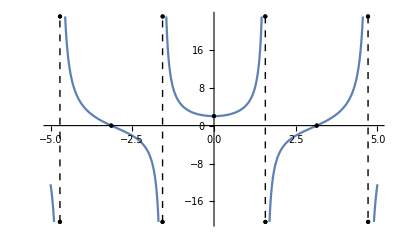

```mathematica
(* частное решение *)
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

{{y[x]→-Cos[x]+Sin[x]}}

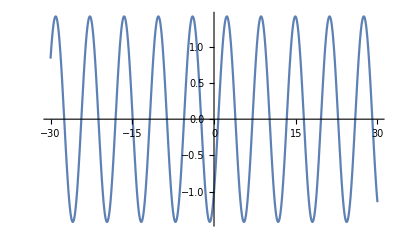

```mathematica
DSolve[y'[x]+y[x]Tan[x]==1/Cos[x],y[x],x] (*Решаем дифференциальное уравнение по функции y независимой переменной x*)
tempRes342 = DSolve[{y'[x]+y[x]Tan[x]==1/Cos[x],y[Pi]==1},y[x],x]
Plot[y[x]/.tempRes342,{x,-30,30}]
```

Самостоятельно выбрав граничные условия найти решение диф. ур-я в символьном виде и изобразить его на графике

```mathematica
complicatedEquasion = {y''[x]-y'[x]+x y[x]==0, y[0]==0, y'[0]==1}
solution1=DSolve[complicatedEquasion,y[x],x] //Simplify
solution2 =NDSolve[complicatedEquasion,y,{x,-5,5}]
Show[Plot[y[x]/.solution1,{x,-5,5}],Plot[y[x]/.solution2,{x,-5,5},PlotStyle->{Dashed,Red}]]
```

{x y[x]-y'[x]+y''[x]==0,y[0]==0,y'[0]==1}

{{y[x]→((-1)^(2/3) ⅇ^(x/2) (-AiryAi[1/4 (-1)^(1/3) (-1+4 x)] AiryBi[-1/4 (-1)^(1/3)]+AiryAi[-1/4 (-1)^(1/3)] AiryBi[1/4 (-1)^(1/3) (-1+4 x)]))/(AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)])}}

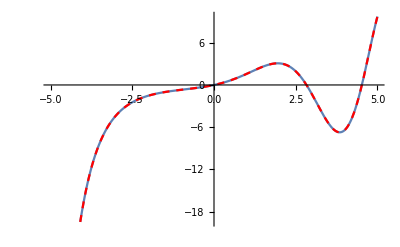

```mathematica
{{y->InterpolatingFunction[…]}}
(* интерполяционная функция (с помощью имеющегося набора данных находятся промежуточные значения) *)
```

## 2.4 Пластинка

```mathematica
Clear["Global *"]
(* вводим ограничения *)
exp1 =x^2
exp2 = 2x+3
exp3 = -x+3

eq1 = exp1==y
eq2 = exp2==y
eq3 = exp3==y
```

x^2

3+2 x

3-x

x^2==y

3+2 x==y

3-x==y

```mathematica
(* Находим координаты центра масс *)
```

{{x→1/2 (-1-√13),y→1/2 (7+√13)},{x→1/2 (-1+√13),y→1/2 (7-√13)}}

1/2 (-1+√13)

1/2 (7-√13)

{{x→0,y→3}}

0

3

{{x→-1,y→1},{x→3,y→9}}

-1

1

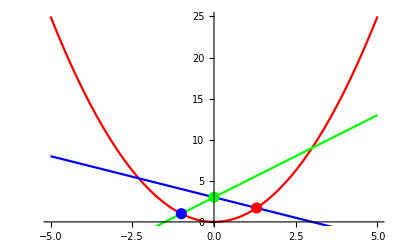

```mathematica
sol1 =Solve[{eq1, eq3}, {x, y}]
x1 = x/.sol1[[2]]
y1 = y/.sol1[[2]]

sol2 = Solve[{eq2, eq3}, {x, y}]
x2 = x /. sol2[[1]]
y2 = y/.sol2[[1]]

sol3 = Solve[{eq1, eq2}, {x, y}]
x3 = x /. sol3[[1]]
y3 = y /. sol3[[1]]
Show[Plot[exp1,{x,-5,5},PlotStyle->Red],Plot[exp2,{x,-5,5},PlotStyle->Green],Plot[exp3,{x,-5,5},PlotStyle->Blue],Epilog->{PointSize[0.02],Red,Point[{x1,y1}],Green,Point[{x2,y2}],Blue,Point[{x3,y3}]}]
```

```mathematica
(* Разбиваем пластинки на маленькие кусочки с помощью интегрирования, таким образом находим площадь *)
```

```mathematica
s = Integrate[1, {x, x1, x2}, {y, exp1, exp2}] + Integrate[1, {x, x2, x3}, {y, exp1,  exp3}] //Simplify
(* находим положение центра масс *)
xc = Simplify[(1/m)(Integrate[(m/s)x, {x, x1, x2}, {y, exp1, exp2}] + Integrate[(m/s)x, {x, x2, x3}, {y, exp1,  exp3}])]
yc = Simplify[(1/m)(Integrate[(m/s)y, {x, x1, x2}, {y, exp1,exp2}] + Integrate[(m/s)y, {x, x2, x3}, {y, exp1,  exp3}])]
```

1/6 (-41-2 √13)

(5 (-293+107 √13))/2172

(5459+184 √13)/2715

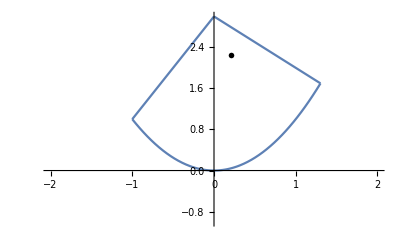

```mathematica
p1 = Plot[exp1, {x, x1, x3}, DisplayFunction->Identity];
p2= Plot[exp2, {x, x2, x3}, DisplayFunction->Identity];
p3= Plot[exp3, {x, x1, x2}, DisplayFunction->Identity];

Show[p1,p2,p3,PlotRange->{{-2,2},{-1,3}},Epilog->{PointSize[0.01],Point[{xc,yc}]},DisplayFunction->$DisplayFunction]
```

```mathematica
(* вычисляем момент инерции пластинки относительно осей и показываем что справедливо отношение Ix + Iy = Iz *)
```

```mathematica
ix = Integrate[(m/s)y^2, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)y^2, {x, x2, x3}, {y, exp1,  exp2}]
iy = Integrate[(m/s)x^2, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)x^2, {x, x2, x3}, {y,  exp1,  exp2}]
iz=  Integrate[(m/s)(x^2+y^2), {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)(x^2+y^2), {x, x2, x3}, {y,  exp1,  exp2}]

ii = Together[ix + iy]
Simplify[ii-iz]
```

-(23 m)/(7 s)+((1037-377 √13) m)/(56 s)

(99 m)/(40 s)-(39 √13 m)/(40 s)

-(251 m)/(70 s)+((5962-2158 √13) m)/(280 s)

-((-2479+1079 √13) m)/(140 s)

0